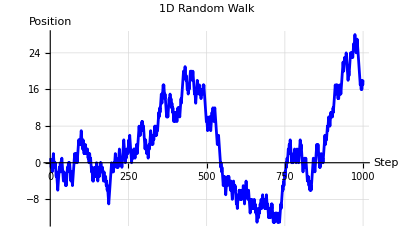

```mathematica
n=1000; (*Number of steps*)
steps=RandomChoice[{-1,1},n]; (*Randomly choose-1 or 1*)
walk=Accumulate[steps]; (*Compute the position at each step*)

ListLinePlot[walk,PlotStyle->Blue,AxesLabel->{"Step","Position"},GridLines->Automatic,PlotLabel->"1D Random Walk"]
```

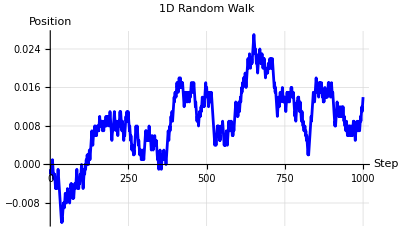

```mathematica
n=1000; (*Number of steps*)
steps=RandomChoice[{-0.001,0.001},n]; (*Randomly choose-1 or 1*)
walk=Accumulate[steps]; (*Compute the position at each step*)

ListLinePlot[walk,PlotStyle->Blue,AxesLabel->{"Step","Position"},GridLines->Automatic,PlotLabel->"1D Random Walk"]
```

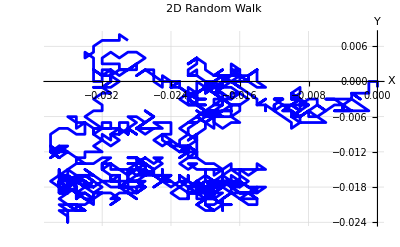

```mathematica
n=1000; (*Number of steps*)
steps=RandomChoice[{{0.001,0},{-0.001,0},{0,0.001},{0,-0.001}, {0.001, 0.001}, {0.001, -0.001}, {-0.001, -0.001}, {-0.001, 0.001}},n]; (*Up,Down,Left,Right*)
walk=Accumulate[steps]; (*Compute the path*)

ListLinePlot[walk,PlotStyle->Blue,AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"2D Random Walk"]
```

```mathematica
n=1000; (*Number of steps*)
steps=RandomChoice[{{0.001,0},{-0.001,0},{0,0.001},{0,-0.001}, {0.001, 0.001}, {0.001, -0.001}, {-0.001, -0.001}, {-0.001, 0.001}},n]; (*Up,Down,Left,Right*)
walk=Accumulate[steps]; 

colors=ColorData["Rainbow"]/@Rescale[Range[Length[walk]]];

Graphics[{Line[Thread[{walk,colors}]]},Axes->True,AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"2D Random Walk with Color-Coded Steps"]
```

-Graphics-

```mathematica
n=1000; (*Number of steps*)
steps=RandomChoice[{{0.001,0},{-0.001,0},{0,0.001},{0,-0.001}, {0.001, 0.001}, {0.001, -0.001}, {-0.001, -0.001}, {-0.001, 0.001}},n]; (*Up,Down,Left,Right*)
walk=Prepend[Accumulate[steps],{0,0}]; (*Include starting position*)

(*Create a color gradient based on the step index*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[walk]]];

Graphics[{Line[Thread[{walk,colors}]]},Axes->True,AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"2D Random Walk with Color-Coded Steps"]
```

-Graphics-

```mathematica
n=1000; (*Number of steps*)
steps=RandomChoice[{{1,0},{-1,0},{0,1},{0,-1}},n]; (*Up,Down,Left,Right*)
walk=Prepend[Accumulate[steps],{0,0}]; (*Include starting position*)

(*Create a color gradient based on the step index*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[walk]]];

Graphics[{Line[Thread[{walk,colors}]]},Axes->True,AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"2D Random Walk with Color-Coded Steps"]
```

-Graphics-

```mathematica
(*Parameters*)n=1000; (*Number of time steps*)
dt=0.01; (*Time step size*)
μ={0.05,0.03}; (*Drift in x and y directions*)
σ={0.2,0.15}; (*Volatility in x and y directions*)

(*Simulate GBM*)
dW=RandomVariate[NormalDistribution[0,Sqrt[dt]],{n,2}]; (*Brownian increments*)
path=Accumulate[μ dt+σ dW,{1}]; (*Compute path with drift and volatility*)

walk=Prepend[path,{0,0}]; (*Include starting position*)

(*Create color gradient based on time step*)
colors=ColorData["Rainbow"]/@Rescale[Range[Length[walk]]];

(*Plot the path with color-coded trajectory*)
Graphics[{Line[Thread[{walk,colors}]]},Axes->True,AxesLabel->{"X","Y"},GridLines->Automatic,PlotLabel->"2D Geometric Brownian Motion with Color Gradient"]
```

Thread::tdlen: Objects of unequal length in {0.2,0.15} {{0.0194892,-0.0273218},{-0.000482429,-0.163798},{-0.0625522,-0.0720163},«46»,{-0.0403797,-0.111421},«950»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Accumulate::nonopt: Options expected (instead of {1}) beyond position 1 in Accumulate[{0.0005+{0.2,0.15} {{0.0194892,-0.0273218},{-0.000482429,-0.163798},«47»,{-0.0403797,-0.111421},«950»},0.0003+{0.2,0.15} {{«20»,-«21»},«50»}},{1}]. An option must be a rule or a list of rules.

Accumulate::nonopt: Options expected (instead of {1}) beyond position 1 in Accumulate[{0,0},{0.0005+{0.2,0.15} {{0.0194892,-0.0273218},{-0.000482429,-0.163798},«47»,{-0.0403797,-0.111421},«950»},0.0003+{0.2,0.15} {«1»}},{1}]. An option must be a rule or a list of rules.

-Graphics-